```mathematica
(*Takehome Assignment Q4*)
```

```mathematica
Remove["Global`*"]
```

```mathematica
Manipulate[Module[{A=NDSolve[{m r[t]^2 θ'[t]==L,m r''[t]-L^2/(m r[t]^3)==-k/r[t]^2,r[0]==p[[2]],r'[0]==v,θ[0]==p[[1]]},{θ[t],r[t]},{t,0,time}]},ParametricPlot[{θ[t],r[t]}/.A,{t,0,time},PlotRange->{{-10,10},{0,5}}]],{{p,{0,1}},Locator},{{time,50},0,100
},{{L,0.1},-10,10},{{m,2},1,10},{k,.5,1},{{v,0},-0.5,0.5}]
```

```mathematica
(*to plot r(θ), i first numerically solved for r[t] and θ[t] and parametrised them. for a given L there exists an r such that dr/dt, i.e. the radial velocity is always 0. this gives a circular orbit of constant r. when dr/dt is not zero the orbits of the two masses around the centre of mass are elliptical.*)
```

```mathematica
Manipulate[Module[{A=NDSolve[{m r[t]^2 θ'[t]==L,m r''[t]-L^2/(m r[t]^3)==-k/r[t]^2,r[0]==Subscript[R, 0],r'[0]==Subscript[v, 0],θ[0]==α},{θ[t]},{t,0,time}]},ParametricPlot[{θ[t]/.A[[1]],t},{t,0,time}]],{{time,20},0,50},{{L,0.1},-10,10},{{m,2},1,10},{k,0.5,1},{{Subscript[v, 0],0},-1,1},{{Subscript[R, 0],1},0.1,5},{{α,0},-4Pi,4Pi}]
```

```mathematica
(*t(θ) comes out like this, because as the object approaches the apsis, it's angular velocity is either highest or lowest, which means it will either cover less angle in more time(steep part) or more angle in less time(flat part)*)
```

```mathematica
NDSolve[{m r[t]^2 θ'[t]==L,m r''[t]-L^2/(m r[t]^3)==-k/r[t]^2,r[0]==R,r'[0]==Subscript[v, 0],θ[0]==0}/.{m->1,L->4,k->0.1,R->5,Subscript[v, 0]->0},{θ[t],r[t]},{t,0,50}]
```

{{θ[t]→InterpolatingFunction[{{0., 50.}}, <>][t],r[t]→InterpolatingFunction[{{0., 50.}}, <>][t]}}

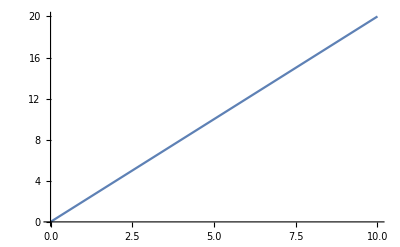

```mathematica
Plot[Integrate[1/2(r[t]/.%[[1,2]])^2 D[(θ[t]/.%[[1,1]]), t],{t,T,T+Δ}/.{T->20}],{Δ,0,10},PlotRange->{{0,10},{0,20}}]
```

```mathematica
(*the expression for area swept by the radius vector in time T to T+Δ is
ΔA= ∫_T^(T+Δ) 1/2 r[t]^2 θ'[t]ⅆt
since m*r[t]^2 θ'[t]=L and angular momentum is a constant of motion, dA/dt is a constant, hence ΔA is independent of T and linearly dependent on Δ.*)
```